```mathematica
GeneratingCurve[A_] := Block[{H, K, f, n, u1, u2, v1, v2},
n = Dimensions[A][[1]];
H = 1/2*(A + ConjugateTranspose[A]);
K = 1/(2*I)*(A - ConjugateTranspose[A]);
f[u1_, u2_, v1_, v2_] := Det[(u1+I*u2)*H + (v1+I*v2)*K + IdentityMatrix[n]];
FullSimplify[f[u1,u2, v1,v2]==0, Assumptions -> Element[u1, Reals] && Element[u2, Reals] && Element[v1, Reals] && Element[v2, Reals]]
];
```

```mathematica
c1 = ComplexExpand[Re[GeneratingCurve[A1]]]
```

16+64 u1+84 u1^2+40 u1^3+5 u1^4-84 u2^2-120 u1 u2^2-30 u1^2 u2^2+5 u2^4-12 v1^2-24 u1 v1^2-10 u1^2 v1^2+10 u2^2 v1^2+v1^4+48 u2 v1 v2+40 u1 u2 v1 v2+12 v2^2+24 u1 v2^2+10 u1^2 v2^2-10 u2^2 v2^2-6 v1^2 v2^2+v2^4==0

```mathematica
c2 = ComplexExpand[Im[GeneratingCurve[A1]]]
```

64 u2+168 u1 u2+120 u1^2 u2+20 u1^3 u2-40 u2^3-20 u1 u2^3-24 u2 v1^2-20 u1 u2 v1^2-24 v1 v2-48 u1 v1 v2-20 u1^2 v1 v2+20 u2^2 v1 v2+4 v1^3 v2+24 u2 v2^2+20 u1 u2 v2^2-4 v1 v2^3==0

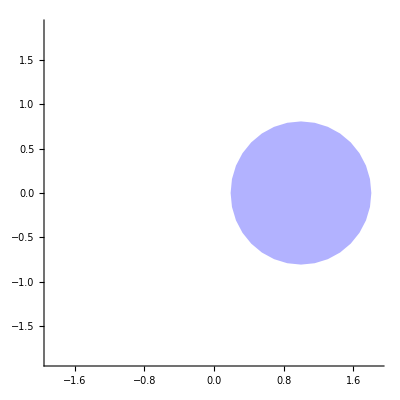

```mathematica
A1 = {
{1, 0, 0, 0},
{1, 1, 0, 0},
{0, 1, 1, 0},
{0, 0, 1, 1}
};
NumericalRangeVisual[A1]
```

```mathematica
c = GeneratingCurve[A1]
```

16+u (64+u (84+5 u (8+u)))+v^4==2 (6+u (12+5 u)) v^2

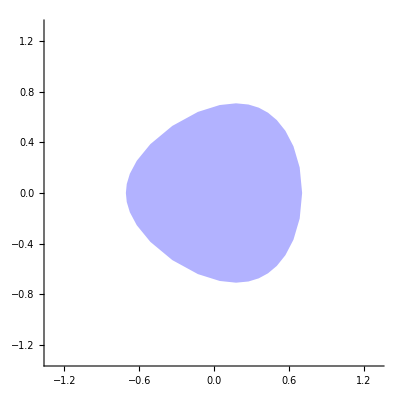

```mathematica
A2 = {
{0, -1/2, 0},
{1/2, 1/Sqrt[2], -1/2},
{0, 1/2, -1/Sqrt[2]}
};
NumericalRangeVisual[A2]
```

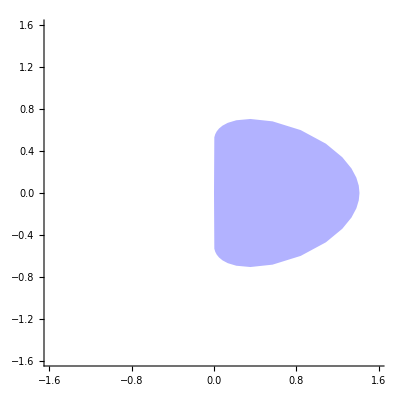

```mathematica
A3 = {
{0, -1/2, 0},
{1/2, 0, -1/2},
{0, 1/2, Sqrt[2]}
};
NumericalRangeVisual[A3]
```

```mathematica
c = GeneratingCurve[A3];
c1 = ComplexExpand[Re[c]];
c2 = ComplexExpand[Im[c]];
```

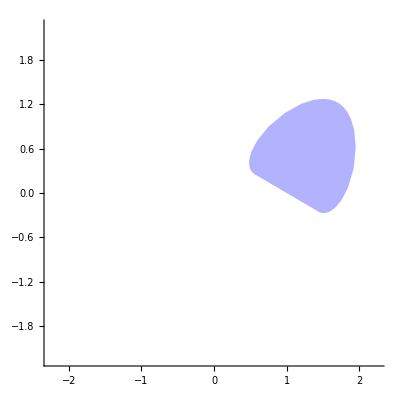

```mathematica
A4 = Exp[I*Pi/3]*{
{0, -1/2, 0},
{1/2, 0, -1/2},
{0, 1/2, Sqrt[2]}
} + IdentityMatrix[3];
NumericalRangeVisual[A4]
```